## Parameter Space

```mathematica
Clear["Global`*"]
np=6/11;nm=3/11;
n0=(1-np-nm);
np+nm+n0
```

1

```mathematica
np2=αp/α np;
nm2=αm/α nm;
n02=1-np2-nm2;
Simplify[np2+nm2+n02]
```

1

```mathematica
αp=i/(m-1)α/np;αm=j/(m-1)α/nm;
α0=α n02/n0;
α=Min[np,nm,n0];
```

```mathematica
α
αp/.i->m-1
αm/.j->m-1
α0/.i->0/.j->0
```

2/11

1/3

2/3

1

```mathematica
m=15;data={};
Clear[i,j]
For[i=0,i≤m-1,i++,
For[j=0,j≤m-1,j++,
If[i+j≤(m-1),AppendTo[data,{np2,nm2}]];
];];
```

```mathematica
Length[data]
m*(m+1)/2
```

120

120

```mathematica
{np,nm}//N
```

{0.545455,0.272727}

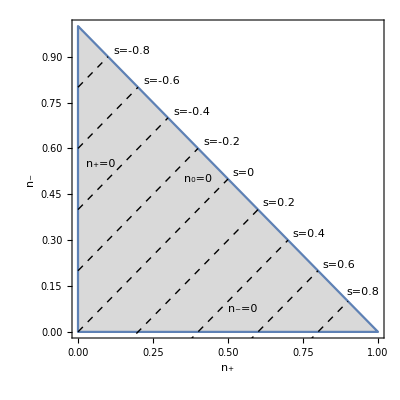

```mathematica
paramspace=RegionPlot[0≤x≤1&&0≤y≤1&&x+y≤1,{x,0,1},{y,0,1},LabelStyle->Directive[16],PlotStyle->LightGray,FrameLabel->{"n_+","n_-"},FrameStyle->Directive[Black],Frame->True,AspectRatio->1,Epilog->{Directive[Dashed],Table[Line[{{0,-s},{(1+s)/2,(1-s)/2}}],{s,-0.8,0.8,0.2}],Style[Text["n_0=0",{0.4,0.5}],16],Style[Text["n_-=0",{0.55,0.075}],16],Style[Text["n_+=0",{0.075,0.55}],16],Style[Text["s=-0.8",{0.18,0.92}],12],Style[Text["s=-0.6",{0.28,0.82}],12],Style[Text["s=-0.4",{0.38,0.72}],12],Style[Text["s=-0.2",{0.48,0.62}],12],Style[Text["s=0",{0.55,0.52}],12],Style[Text["s=0.2",{0.67,0.42}],12],Style[Text["s=0.4",{0.77,0.32}],12],Style[Text["s=0.6",{0.87,0.22}],12],Style[Text["s=0.8",{0.95,0.13}],12]}]
```

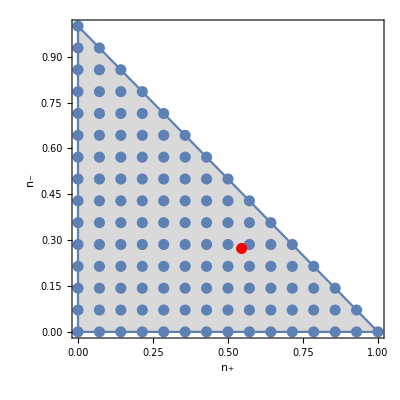

```mathematica
paramspacegrid=Show[{paramspace,ListPlot[data,PlotStyle->Directive[PointSize[0.02]]]},Epilog->{Directive[Red,PointSize[0.02]],Point[{np,nm}]}]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/Notes/Figures"];
Export["paramspace.pdf",paramspace]
Export["paramspacegrid.pdf",paramspacegrid]
```

paramspace.pdf

paramspacegrid.pdf

```mathematica
Clear[grid,p1]
SetDirectory[NotebookDirectory[]];
grid=Import["griddump","List"];
grid=ToExpression[StringReplace[StringReplace[grid,"["->"{"],"]"->"}"]];
```

```mathematica
p1=ListPlot3D[{Table[Join[grid⟦i1⟧⟦1;;2⟧,{grid⟦i1⟧⟦3⟧}],{i1,1,Length[grid]}],Table[Join[grid⟦i1⟧⟦1;;2⟧,{grid⟦i1⟧⟦4⟧}],{i1,1,Length[grid]}],Table[Join[grid⟦i1⟧⟦1;;2⟧,{grid⟦i1⟧⟦3⟧}],{i1,1,Length[grid]}],Table[Join[grid⟦i1⟧⟦1;;2⟧,{0}],{i1,1,Length[grid]}]},PlotRange->All]
```

-Graphics3D-

```mathematica
p1=ListPlot3D[{Table[Join[grid⟦i1⟧⟦1;;2⟧,{Abs[grid⟦i1⟧⟦3⟧-grid⟦i1⟧⟦4⟧]}],{i1,1,Length[grid]}]},PlotRange->All]
```

-Graphics3D-

```mathematica
(*Interpolation[Table[{{grid⟦i1⟧⟦1⟧,grid⟦i1⟧⟦2⟧},grid⟦i1⟧⟦3⟧},{i1,1,Length[grid]}]]*)
```

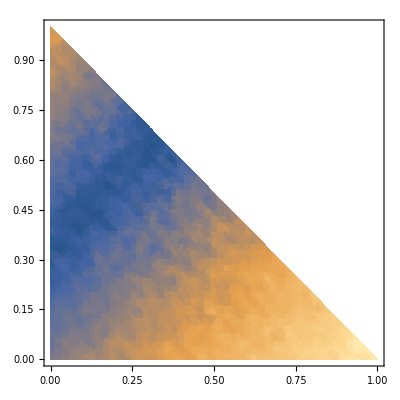

```mathematica
ListDensityPlot[Table[Join[grid⟦i1⟧⟦1;;2⟧,{Abs[grid⟦i1⟧⟦3⟧-grid⟦i1⟧⟦4⟧]}],{i1,1,Length[grid]}]]
```

```mathematica
ListPlot3D[Table[Join[grid⟦i1⟧⟦1;;2⟧,{Abs[grid⟦i1⟧⟦3⟧-grid⟦i1⟧⟦4⟧]}],{i1,1,Length[grid]}],Mesh->False]
```

-Graphics3D-